```mathematica
Quit[]
```

```mathematica
f[t_]=Series[F[t],{t,0,10}]//Normal
```

F[0]+t F'[0]+1/2 t^2 F''[0]+1/6 t^3 F^(3)[0]+1/24 t^4 F^(4)[0]+1/120 t^5 F^(5)[0]+1/720 t^6 F^(6)[0]+(t^7 F^(7)[0])/5040+(t^8 F^(8)[0])/40320+(t^9 F^(9)[0])/362880+(t^10 F^(10)[0])/3628800

```mathematica
(f[dt]-f[-dt])/(2 dt)+O[dt]^3
```

F'[0]+1/6 F^(3)[0] dt^2+O[dt]^3

```mathematica
(k0 f[0]+k1 f[-dt]+k2 f[-2dt])/dt+O[dt]^3//Simplify
```

((k0+k1+k2) F[0])/dt-(k1+2 k2) F'[0]+1/2 (k1+4 k2) F''[0] dt-1/6 ((k1+8 k2) F^(3)[0]) dt^2+O[dt]^3

```mathematica
k0=-k1-k2;
```

```mathematica
(k0 f[0]+k1 f[-dt]+k2 f[-2dt])/dt+O[dt]^3//Simplify
```

-(k1+2 k2) F'[0]+1/2 (k1+4 k2) F''[0] dt-1/6 ((k1+8 k2) F^(3)[0]) dt^2+O[dt]^3

```mathematica
k1=-4 k2;
```

```mathematica
(k0 f[0]+k1 f[-dt]+k2 f[-2dt])/dt+O[dt]^3//Simplify
```

2 k2 F'[0]-2/3 (k2 F^(3)[0]) dt^2+O[dt]^3

```mathematica
k2=1/2;
```

```mathematica
k0
k1
k2
```

3/2

-2

1/2

```mathematica
(3/2 f[0]-2 f[-dt]+1/2 f[-2dt])/dt+O[dt]^3//Simplify
```

F'[0]-1/3 F^(3)[0] dt^2+O[dt]^3

```mathematica
Quit[]
```

```mathematica
wave=1/c^2D[F[t,r],{t,2}]-1/r^2 D[r^2 D[F[t,r],r],r]-S[t,r]//Simplify
```

-S[t,r]-(2 F^(0,1)[t,r])/r-F^(0,2)[t,r]+(F^(2,0)[t,r])/c^2

```mathematica
p=c dt/dr;
```

```mathematica
eq[n_,i_]=(-(u[n+1,i+1]+u[n+1,i-1])+2 (1+2/p^2) u[n+1,i]-2 (u[n,i+1]+u[n,i-1]-2 (1-2/p^2) u[n,i])-(u[n-1,i+1]+u[n-1,i-1]-2 (1+2/p^2) u[n-1,i])-4 c^2 dt^2/p^2 (2/r[i] (u[n,i+1]-u[n,i-1])/(2 dr)+σ[n,i]))/dr^2
```

1/dr^2(-u[-1+n,-1+i]+2 (1+(2 dr^2)/(c^2 dt^2)) u[-1+n,i]-u[-1+n,1+i]-2 (u[n,-1+i]-2 (1-(2 dr^2)/(c^2 dt^2)) u[n,i]+u[n,1+i])-u[1+n,-1+i]+2 (1+(2 dr^2)/(c^2 dt^2)) u[1+n,i]-u[1+n,1+i]-4 dr^2 ((-u[n,-1+i]+u[n,1+i])/(dr r[i])+σ[n,i]))

```mathematica
(*r[i_]=i dr;*)
```

```mathematica
F[t_,r_]=(Series[f[t0+ϵ (t-t0),r0+ϵ(r-r0)],{ϵ,0,5}]//Normal)/.ϵ->1
S[t_,r_]=(Series[s[t0+ϵ (t-t0),r0+ϵ(r-r0)],{ϵ,0,5}]//Normal)/.ϵ->1
```

f[t0,r0]+(r-r0) f^(0,1)[t0,r0]+1/2 (r-r0)^2 f^(0,2)[t0,r0]+1/6 (r-r0)^3 f^(0,3)[t0,r0]+1/24 (r-r0)^4 f^(0,4)[t0,r0]+1/120 (r-r0)^5 f^(0,5)[t0,r0]+(t-t0) f^(1,0)[t0,r0]+(r-r0) (t-t0) f^(1,1)[t0,r0]+1/2 (r-r0)^2 (t-t0) f^(1,2)[t0,r0]+1/6 (r-r0)^3 (t-t0) f^(1,3)[t0,r0]+1/24 (r-r0)^4 (t-t0) f^(1,4)[t0,r0]+1/2 (t-t0)^2 f^(2,0)[t0,r0]+1/2 (r-r0) (t-t0)^2 f^(2,1)[t0,r0]+1/4 (r-r0)^2 (t-t0)^2 f^(2,2)[t0,r0]+1/12 (r-r0)^3 (t-t0)^2 f^(2,3)[t0,r0]+1/6 (t-t0)^3 f^(3,0)[t0,r0]+1/6 (r-r0) (t-t0)^3 f^(3,1)[t0,r0]+1/12 (r-r0)^2 (t-t0)^3 f^(3,2)[t0,r0]+1/24 (t-t0)^4 f^(4,0)[t0,r0]+1/24 (r-r0) (t-t0)^4 f^(4,1)[t0,r0]+1/120 (t-t0)^5 f^(5,0)[t0,r0]

s[t0,r0]+(r-r0) s^(0,1)[t0,r0]+1/2 (r-r0)^2 s^(0,2)[t0,r0]+1/6 (r-r0)^3 s^(0,3)[t0,r0]+1/24 (r-r0)^4 s^(0,4)[t0,r0]+1/120 (r-r0)^5 s^(0,5)[t0,r0]+(t-t0) s^(1,0)[t0,r0]+(r-r0) (t-t0) s^(1,1)[t0,r0]+1/2 (r-r0)^2 (t-t0) s^(1,2)[t0,r0]+1/6 (r-r0)^3 (t-t0) s^(1,3)[t0,r0]+1/24 (r-r0)^4 (t-t0) s^(1,4)[t0,r0]+1/2 (t-t0)^2 s^(2,0)[t0,r0]+1/2 (r-r0) (t-t0)^2 s^(2,1)[t0,r0]+1/4 (r-r0)^2 (t-t0)^2 s^(2,2)[t0,r0]+1/12 (r-r0)^3 (t-t0)^2 s^(2,3)[t0,r0]+1/6 (t-t0)^3 s^(3,0)[t0,r0]+1/6 (r-r0) (t-t0)^3 s^(3,1)[t0,r0]+1/12 (r-r0)^2 (t-t0)^3 s^(3,2)[t0,r0]+1/24 (t-t0)^4 s^(4,0)[t0,r0]+1/24 (r-r0) (t-t0)^4 s^(4,1)[t0,r0]+1/120 (t-t0)^5 s^(5,0)[t0,r0]

```mathematica
wave0=wave/.{r->r0,t->t0}
```

-s[t0,r0]-(2 f^(0,1)[t0,r0])/r0-f^(0,2)[t0,r0]+(f^(2,0)[t0,r0])/c^2

```mathematica
sol=Solve[wave0==0,Derivative[2,0][f][t0,r0]]//Flatten
```

{f^(2,0)[t0,r0]→(c^2 (r0 s[t0,r0]+2 f^(0,1)[t0,r0]+r0 f^(0,2)[t0,r0]))/r0}

```mathematica
u[n_,i_]:=F[t0+n dt,r0+i dr]
σ[n_,i_]:=S[t0+n dt,r0+i dr]
```

```mathematica
((eq[0,0]/.{r[0]->r0,dr->ϵ dr,dt->ϵ dt}))//Simplify
```

-4 s[t0,r0]-(8 f^(0,1)[t0,r0])/r0-4 f^(0,2)[t0,r0]-(4 dr^2 ϵ^2 f^(0,3)[t0,r0])/(3 r0)-1/3 dr^2 ϵ^2 f^(0,4)[t0,r0]-(dr^4 ϵ^4 f^(0,5)[t0,r0])/(15 r0)+(4 f^(2,0)[t0,r0])/c^2-dt^2 ϵ^2 f^(2,2)[t0,r0]+(dt^2 ϵ^2 f^(4,0)[t0,r0])/(3 c^2)

```mathematica
((eq[0,0]/.{r[0]->r0,dr->ϵ dr,dt->ϵ dt})+O[ϵ]^4)/.sol//Simplify
```

1/3 (-(4 dr^2 f^(0,3)[t0,r0])/r0-dr^2 f^(0,4)[t0,r0]+dt^2 (-3 f^(2,2)[t0,r0]+(f^(4,0)[t0,r0])/c^2)) ϵ^2+O[ϵ]^4

```mathematica
Quit[]
```

```mathematica
σ[n_,i_]=0;
```

```mathematica
p=c dt/dr;
c=1;
```

```mathematica
eq[i_]=(-(u[n+1,i+1]+u[n+1,i-1])+2 (1+2/p^2) u[n+1,i]-2 (u[n,i+1]+u[n,i-1]-2 (1-2/p^2) u[n,i])-(u[n-1,i+1]+u[n-1,i-1]-2 (1+2/p^2) u[n-1,i])-4 c^2 dt^2/p^2 (2/r[i] (u[n,i+1]-u[n,i-1])/(2 dr)+σ[n,i]))
```

-u[-1+n,-1+i]+2 (1+(2 dr^2)/dt^2) u[-1+n,i]-u[-1+n,1+i]-(4 dr (-u[n,-1+i]+u[n,1+i]))/r[i]-2 (u[n,-1+i]-2 (1-(2 dr^2)/dt^2) u[n,i]+u[n,1+i])-u[1+n,-1+i]+2 (1+(2 dr^2)/dt^2) u[1+n,i]-u[1+n,1+i]

```mathematica
r[i_]=(i+1/2) dr;
```

```mathematica
imax=1000;
```

```mathematica
eqs=Table[eq[i],{i,0,imax}];
vars=Table[u[n+1,i],{i,0,imax}];
```

```mathematica
coefs=CoefficientArrays[eqs,vars]//Simplify
```

{SparseArray[<1001>, {1001}],SparseArray[…]}

```mathematica
(b=coefs[[1]])//MatrixForm
(A=coefs[[2]])//MatrixForm
```

(1)
 |  |  |  |

(1)
 |  |  |  |

```mathematica
A.vars+b-eqs//Simplify//Union
```

{0}

```mathematica
r[-1]
r[0]
```

-dr/2

dr/2

```mathematica
u[n,-1]=u[n,0] (*reg*)
u[n-1,-1]=u[n-1,0] (*reg*)
u[n+1,-1]=u[n+1,0] (*reg*)
```

u[n,0]

u[-1+n,0]

u[1+n,0]

```mathematica
b[[1;;10]]//MatrixForm
```

(-u[-1+n,0]+(2+(4 dr^2)/dt^2) u[-1+n,0]-u[-1+n,1]+10 u[n,0]-(8 dr^2 u[n,0])/dt^2-10 u[n,1]-u[1+n,0]
-u[-1+n,0]+(2+(4 dr^2)/dt^2) u[-1+n,1]-u[-1+n,2]+2/3 u[n,0]+4 u[n,1]-(8 dr^2 u[n,1])/dt^2-14/3 u[n,2]
-u[-1+n,1]+(2+(4 dr^2)/dt^2) u[-1+n,2]-u[-1+n,3]-2/5 u[n,1]+4 u[n,2]-(8 dr^2 u[n,2])/dt^2-18/5 u[n,3]
-u[-1+n,2]+(2+(4 dr^2)/dt^2) u[-1+n,3]-u[-1+n,4]-6/7 u[n,2]+4 u[n,3]-(8 dr^2 u[n,3])/dt^2-22/7 u[n,4]
-u[-1+n,3]+(2+(4 dr^2)/dt^2) u[-1+n,4]-u[-1+n,5]-10/9 u[n,3]+4 u[n,4]-(8 dr^2 u[n,4])/dt^2-26/9 u[n,5]
-u[-1+n,4]+(2+(4 dr^2)/dt^2) u[-1+n,5]-u[-1+n,6]-14/11 u[n,4]+4 u[n,5]-(8 dr^2 u[n,5])/dt^2-30/11 u[n,6]
-u[-1+n,5]+(2+(4 dr^2)/dt^2) u[-1+n,6]-u[-1+n,7]-18/13 u[n,5]+4 u[n,6]-(8 dr^2 u[n,6])/dt^2-34/13 u[n,7]
-u[-1+n,6]+(2+(4 dr^2)/dt^2) u[-1+n,7]-u[-1+n,8]-22/15 u[n,6]+4 u[n,7]-(8 dr^2 u[n,7])/dt^2-38/15 u[n,8]
-u[-1+n,7]+(2+(4 dr^2)/dt^2) u[-1+n,8]-u[-1+n,9]-26/17 u[n,7]+4 u[n,8]-(8 dr^2 u[n,8])/dt^2-42/17 u[n,9]
-u[-1+n,8]+(2+(4 dr^2)/dt^2) u[-1+n,9]-u[-1+n,10]-30/19 u[n,8]+4 u[n,9]-(8 dr^2 u[n,9])/dt^2-46/19 u[n,10])

```mathematica
out[n_]=(3/2 u[n,imax]-2u[n-1,imax]+1/2 u[n-2,imax])/dt+(u[n,imax+1]-u[n,imax-1])/(2 dr)+0*u[n,imax]/r[imax]
```

(1/2 u[-2+n,1000]-2 u[-1+n,1000]+3/2 u[n,1000])/dt+(-u[n,999]+u[n,1001])/(2 dr)

```mathematica
out[n-1]
out[n+1]
```

(1/2 u[-3+n,1000]-2 u[-2+n,1000]+3/2 u[-1+n,1000])/dt+(-u[-1+n,999]+u[-1+n,1001])/(2 dr)

(1/2 u[-1+n,1000]-2 u[n,1000]+3/2 u[1+n,1000])/dt+(-u[1+n,999]+u[1+n,1001])/(2 dr)

```mathematica
sol=Solve[{out[n]==0,out[n-1]==0,out[n+1]==0},{u[n-1,imax+1],u[n,imax+1],u[n+1,imax+1]}]//Simplify
```

{{u[-1+n,1001]→(-dr u[-3+n,1000]+4 dr u[-2+n,1000]+dt u[-1+n,999]-3 dr u[-1+n,1000])/dt,u[n,1001]→(-dr u[-2+n,1000]+4 dr u[-1+n,1000]+dt u[n,999]-3 dr u[n,1000])/dt,u[1+n,1001]→(-dr u[-1+n,1000]+4 dr u[n,1000]+dt u[1+n,999]-3 dr u[1+n,1000])/dt}}

```mathematica
u[-1+n,imax+1]=u[-1+n,imax+1]/.sol[[1]]
u[n,imax+1]=u[n,imax+1]/.sol[[1]]
u[1+n,imax+1]=u[1+n,imax+1]/.sol[[1]]
```

(-dr u[-3+n,1000]+4 dr u[-2+n,1000]+dt u[-1+n,999]-3 dr u[-1+n,1000])/dt

(-dr u[-2+n,1000]+4 dr u[-1+n,1000]+dt u[n,999]-3 dr u[n,1000])/dt

(-dr u[-1+n,1000]+4 dr u[n,1000]+dt u[1+n,999]-3 dr u[1+n,1000])/dt

```mathematica
out[n]//Simplify
out[n-1]//Simplify
out[n+1]//Simplify
```

0

0

0

```mathematica
coefs=CoefficientArrays[eqs,vars]//Simplify
(b=coefs[[1]]);
(A=coefs[[2]]);
```

{SparseArray[<1001>, {1001}],SparseArray[…]}

```mathematica
A.vars+b-eqs//Simplify//Union
```

{0}

```mathematica
b[[imax-5;;imax+1]]//MatrixForm
```

(-u[-1+n,993]+(2+(4 dr^2)/dt^2) u[-1+n,994]-u[-1+n,995]-(3970 u[n,993])/1989+4 u[n,994]-(8 dr^2 u[n,994])/dt^2-(3986 u[n,995])/1989
-u[-1+n,994]+(2+(4 dr^2)/dt^2) u[-1+n,995]-u[-1+n,996]-(3974 u[n,994])/1991+4 u[n,995]-(8 dr^2 u[n,995])/dt^2-(3990 u[n,996])/1991
-u[-1+n,995]+(2+(4 dr^2)/dt^2) u[-1+n,996]-u[-1+n,997]-(3978 u[n,995])/1993+4 u[n,996]-(8 dr^2 u[n,996])/dt^2-(3994 u[n,997])/1993
-u[-1+n,996]+(2+(4 dr^2)/dt^2) u[-1+n,997]-u[-1+n,998]-(3982 u[n,996])/1995+4 u[n,997]-(8 dr^2 u[n,997])/dt^2-(3998 u[n,998])/1995
-u[-1+n,997]+(2+(4 dr^2)/dt^2) u[-1+n,998]-u[-1+n,999]-(3986 u[n,997])/1997+4 u[n,998]-(8 dr^2 u[n,998])/dt^2-(4002 u[n,999])/1997
-u[-1+n,998]+(2+(4 dr^2)/dt^2) u[-1+n,999]-u[-1+n,1000]-(3990 u[n,998])/1999+4 u[n,999]-(8 dr^2 u[n,999])/dt^2-(4006 u[n,1000])/1999
(dr u[-3+n,1000])/dt-(3994 dr u[-2+n,1000])/(2001 dt)-2 u[-1+n,999]+2 u[-1+n,1000]+(4 dr^2 u[-1+n,1000])/dt^2-(8036 dr u[-1+n,1000])/(2001 dt)-4 u[n,999]+4 u[n,1000]-(8 dr^2 u[n,1000])/dt^2+(1342 dr u[n,1000])/(667 dt))

```mathematica
vars[[-1]]
```

u[1+n,1000]

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False]
```

CheckMachineUnderflow→False

```mathematica
(*Initial conditions*)
Do[u[0,i]=Exp[-1/2 (r[i]-20)^2],{i,0,imax}]
```

```mathematica
Do[u[-1,i]=u[1,i],{i,0,imax}]
```

```mathematica
u[-2,imax]=0;
u[-3,imax]=0;
```

```mathematica
dr=0.1;
dt=0.08;
```

```mathematica
e0=eqs/.{n->0};
```

```mathematica
v1=vars/.{n->0}
```

{u[1,0],u[1,1],u[1,2],u[1,3],u[1,4],u[1,5],u[1,6],u[1,7],u[1,8],u[1,9],u[1,10],u[1,11],u[1,12],u[1,13],u[1,14],u[1,15],u[1,16],u[1,17],u[1,18],u[1,19],u[1,20],u[1,21],u[1,22],u[1,23],u[1,24],u[1,25],u[1,26],u[1,27],u[1,28],u[1,29],u[1,30],u[1,31],u[1,32],u[1,33],u[1,34],u[1,35],u[1,36],u[1,37],u[1,38],u[1,39],u[1,40],u[1,41],u[1,42],u[1,43],u[1,44],u[1,45],u[1,46],u[1,47],u[1,48],u[1,49],u[1,50],u[1,51],u[1,52],u[1,53],u[1,54],u[1,55],u[1,56],u[1,57],u[1,58],u[1,59],u[1,60],u[1,61],u[1,62],u[1,63],u[1,64],u[1,65],u[1,66],u[1,67],u[1,68],u[1,69],u[1,70],u[1,71],u[1,72],u[1,73],u[1,74],u[1,75],u[1,76],u[1,77],u[1,78],u[1,79],u[1,80],u[1,81],u[1,82],u[1,83],u[1,84],u[1,85],u[1,86],u[1,87],u[1,88],u[1,89],u[1,90],u[1,91],u[1,92],u[1,93],u[1,94],u[1,95],u[1,96],u[1,97],u[1,98],u[1,99],u[1,100],u[1,101],u[1,102],u[1,103],u[1,104],u[1,105],u[1,106],u[1,107],u[1,108],u[1,109],u[1,110],u[1,111],u[1,112],u[1,113],u[1,114],u[1,115],u[1,116],u[1,117],u[1,118],u[1,119],u[1,120],u[1,121],u[1,122],u[1,123],u[1,124],u[1,125],u[1,126],u[1,127],u[1,128],u[1,129],u[1,130],u[1,131],u[1,132],u[1,133],u[1,134],u[1,135],u[1,136],u[1,137],u[1,138],u[1,139],u[1,140],u[1,141],u[1,142],u[1,143],u[1,144],u[1,145],u[1,146],u[1,147],u[1,148],u[1,149],u[1,150],u[1,151],u[1,152],u[1,153],u[1,154],u[1,155],u[1,156],u[1,157],u[1,158],u[1,159],u[1,160],u[1,161],u[1,162],u[1,163],u[1,164],u[1,165],u[1,166],u[1,167],u[1,168],u[1,169],u[1,170],u[1,171],u[1,172],u[1,173],u[1,174],u[1,175],u[1,176],u[1,177],u[1,178],u[1,179],u[1,180],u[1,181],u[1,182],u[1,183],u[1,184],u[1,185],u[1,186],u[1,187],u[1,188],u[1,189],u[1,190],u[1,191],u[1,192],u[1,193],u[1,194],u[1,195],u[1,196],u[1,197],u[1,198],u[1,199],u[1,200],u[1,201],u[1,202],u[1,203],u[1,204],u[1,205],u[1,206],u[1,207],u[1,208],u[1,209],u[1,210],u[1,211],u[1,212],u[1,213],u[1,214],u[1,215],u[1,216],u[1,217],u[1,218],u[1,219],u[1,220],u[1,221],u[1,222],u[1,223],u[1,224],u[1,225],u[1,226],u[1,227],u[1,228],u[1,229],u[1,230],u[1,231],u[1,232],u[1,233],u[1,234],u[1,235],u[1,236],u[1,237],u[1,238],u[1,239],u[1,240],u[1,241],u[1,242],u[1,243],u[1,244],u[1,245],u[1,246],u[1,247],u[1,248],u[1,249],u[1,250],u[1,251],u[1,252],u[1,253],u[1,254],u[1,255],u[1,256],u[1,257],u[1,258],u[1,259],u[1,260],u[1,261],u[1,262],u[1,263],u[1,264],u[1,265],u[1,266],u[1,267],u[1,268],u[1,269],u[1,270],u[1,271],u[1,272],u[1,273],u[1,274],u[1,275],u[1,276],u[1,277],u[1,278],u[1,279],u[1,280],u[1,281],u[1,282],u[1,283],u[1,284],u[1,285],u[1,286],u[1,287],u[1,288],u[1,289],u[1,290],u[1,291],u[1,292],u[1,293],u[1,294],u[1,295],u[1,296],u[1,297],u[1,298],u[1,299],u[1,300],u[1,301],u[1,302],u[1,303],u[1,304],u[1,305],u[1,306],u[1,307],u[1,308],u[1,309],u[1,310],u[1,311],u[1,312],u[1,313],u[1,314],u[1,315],u[1,316],u[1,317],u[1,318],u[1,319],u[1,320],u[1,321],u[1,322],u[1,323],u[1,324],u[1,325],u[1,326],u[1,327],u[1,328],u[1,329],u[1,330],u[1,331],u[1,332],u[1,333],u[1,334],u[1,335],u[1,336],u[1,337],u[1,338],u[1,339],u[1,340],u[1,341],u[1,342],u[1,343],u[1,344],u[1,345],u[1,346],u[1,347],u[1,348],u[1,349],u[1,350],u[1,351],u[1,352],u[1,353],u[1,354],u[1,355],u[1,356],u[1,357],u[1,358],u[1,359],u[1,360],u[1,361],u[1,362],u[1,363],u[1,364],u[1,365],u[1,366],u[1,367],u[1,368],u[1,369],u[1,370],u[1,371],u[1,372],u[1,373],u[1,374],u[1,375],u[1,376],u[1,377],u[1,378],u[1,379],u[1,380],u[1,381],u[1,382],u[1,383],u[1,384],u[1,385],u[1,386],u[1,387],u[1,388],u[1,389],u[1,390],u[1,391],u[1,392],u[1,393],u[1,394],u[1,395],u[1,396],u[1,397],u[1,398],u[1,399],u[1,400],u[1,401],u[1,402],u[1,403],u[1,404],u[1,405],u[1,406],u[1,407],u[1,408],u[1,409],u[1,410],u[1,411],u[1,412],u[1,413],u[1,414],u[1,415],u[1,416],u[1,417],u[1,418],u[1,419],u[1,420],u[1,421],u[1,422],u[1,423],u[1,424],u[1,425],u[1,426],u[1,427],u[1,428],u[1,429],u[1,430],u[1,431],u[1,432],u[1,433],u[1,434],u[1,435],u[1,436],u[1,437],u[1,438],u[1,439],u[1,440],u[1,441],u[1,442],u[1,443],u[1,444],u[1,445],u[1,446],u[1,447],u[1,448],u[1,449],u[1,450],u[1,451],u[1,452],u[1,453],u[1,454],u[1,455],u[1,456],u[1,457],u[1,458],u[1,459],u[1,460],u[1,461],u[1,462],u[1,463],u[1,464],u[1,465],u[1,466],u[1,467],u[1,468],u[1,469],u[1,470],u[1,471],u[1,472],u[1,473],u[1,474],u[1,475],u[1,476],u[1,477],u[1,478],u[1,479],u[1,480],u[1,481],u[1,482],u[1,483],u[1,484],u[1,485],u[1,486],u[1,487],u[1,488],u[1,489],u[1,490],u[1,491],u[1,492],u[1,493],u[1,494],u[1,495],u[1,496],u[1,497],u[1,498],u[1,499],u[1,500],u[1,501],u[1,502],u[1,503],u[1,504],u[1,505],u[1,506],u[1,507],u[1,508],u[1,509],u[1,510],u[1,511],u[1,512],u[1,513],u[1,514],u[1,515],u[1,516],u[1,517],u[1,518],u[1,519],u[1,520],u[1,521],u[1,522],u[1,523],u[1,524],u[1,525],u[1,526],u[1,527],u[1,528],u[1,529],u[1,530],u[1,531],u[1,532],u[1,533],u[1,534],u[1,535],u[1,536],u[1,537],u[1,538],u[1,539],u[1,540],u[1,541],u[1,542],u[1,543],u[1,544],u[1,545],u[1,546],u[1,547],u[1,548],u[1,549],u[1,550],u[1,551],u[1,552],u[1,553],u[1,554],u[1,555],u[1,556],u[1,557],u[1,558],u[1,559],u[1,560],u[1,561],u[1,562],u[1,563],u[1,564],u[1,565],u[1,566],u[1,567],u[1,568],u[1,569],u[1,570],u[1,571],u[1,572],u[1,573],u[1,574],u[1,575],u[1,576],u[1,577],u[1,578],u[1,579],u[1,580],u[1,581],u[1,582],u[1,583],u[1,584],u[1,585],u[1,586],u[1,587],u[1,588],u[1,589],u[1,590],u[1,591],u[1,592],u[1,593],u[1,594],u[1,595],u[1,596],u[1,597],u[1,598],u[1,599],u[1,600],u[1,601],u[1,602],u[1,603],u[1,604],u[1,605],u[1,606],u[1,607],u[1,608],u[1,609],u[1,610],u[1,611],u[1,612],u[1,613],u[1,614],u[1,615],u[1,616],u[1,617],u[1,618],u[1,619],u[1,620],u[1,621],u[1,622],u[1,623],u[1,624],u[1,625],u[1,626],u[1,627],u[1,628],u[1,629],u[1,630],u[1,631],u[1,632],u[1,633],u[1,634],u[1,635],u[1,636],u[1,637],u[1,638],u[1,639],u[1,640],u[1,641],u[1,642],u[1,643],u[1,644],u[1,645],u[1,646],u[1,647],u[1,648],u[1,649],u[1,650],u[1,651],u[1,652],u[1,653],u[1,654],u[1,655],u[1,656],u[1,657],u[1,658],u[1,659],u[1,660],u[1,661],u[1,662],u[1,663],u[1,664],u[1,665],u[1,666],u[1,667],u[1,668],u[1,669],u[1,670],u[1,671],u[1,672],u[1,673],u[1,674],u[1,675],u[1,676],u[1,677],u[1,678],u[1,679],u[1,680],u[1,681],u[1,682],u[1,683],u[1,684],u[1,685],u[1,686],u[1,687],u[1,688],u[1,689],u[1,690],u[1,691],u[1,692],u[1,693],u[1,694],u[1,695],u[1,696],u[1,697],u[1,698],u[1,699],u[1,700],u[1,701],u[1,702],u[1,703],u[1,704],u[1,705],u[1,706],u[1,707],u[1,708],u[1,709],u[1,710],u[1,711],u[1,712],u[1,713],u[1,714],u[1,715],u[1,716],u[1,717],u[1,718],u[1,719],u[1,720],u[1,721],u[1,722],u[1,723],u[1,724],u[1,725],u[1,726],u[1,727],u[1,728],u[1,729],u[1,730],u[1,731],u[1,732],u[1,733],u[1,734],u[1,735],u[1,736],u[1,737],u[1,738],u[1,739],u[1,740],u[1,741],u[1,742],u[1,743],u[1,744],u[1,745],u[1,746],u[1,747],u[1,748],u[1,749],u[1,750],u[1,751],u[1,752],u[1,753],u[1,754],u[1,755],u[1,756],u[1,757],u[1,758],u[1,759],u[1,760],u[1,761],u[1,762],u[1,763],u[1,764],u[1,765],u[1,766],u[1,767],u[1,768],u[1,769],u[1,770],u[1,771],u[1,772],u[1,773],u[1,774],u[1,775],u[1,776],u[1,777],u[1,778],u[1,779],u[1,780],u[1,781],u[1,782],u[1,783],u[1,784],u[1,785],u[1,786],u[1,787],u[1,788],u[1,789],u[1,790],u[1,791],u[1,792],u[1,793],u[1,794],u[1,795],u[1,796],u[1,797],u[1,798],u[1,799],u[1,800],u[1,801],u[1,802],u[1,803],u[1,804],u[1,805],u[1,806],u[1,807],u[1,808],u[1,809],u[1,810],u[1,811],u[1,812],u[1,813],u[1,814],u[1,815],u[1,816],u[1,817],u[1,818],u[1,819],u[1,820],u[1,821],u[1,822],u[1,823],u[1,824],u[1,825],u[1,826],u[1,827],u[1,828],u[1,829],u[1,830],u[1,831],u[1,832],u[1,833],u[1,834],u[1,835],u[1,836],u[1,837],u[1,838],u[1,839],u[1,840],u[1,841],u[1,842],u[1,843],u[1,844],u[1,845],u[1,846],u[1,847],u[1,848],u[1,849],u[1,850],u[1,851],u[1,852],u[1,853],u[1,854],u[1,855],u[1,856],u[1,857],u[1,858],u[1,859],u[1,860],u[1,861],u[1,862],u[1,863],u[1,864],u[1,865],u[1,866],u[1,867],u[1,868],u[1,869],u[1,870],u[1,871],u[1,872],u[1,873],u[1,874],u[1,875],u[1,876],u[1,877],u[1,878],u[1,879],u[1,880],u[1,881],u[1,882],u[1,883],u[1,884],u[1,885],u[1,886],u[1,887],u[1,888],u[1,889],u[1,890],u[1,891],u[1,892],u[1,893],u[1,894],u[1,895],u[1,896],u[1,897],u[1,898],u[1,899],u[1,900],u[1,901],u[1,902],u[1,903],u[1,904],u[1,905],u[1,906],u[1,907],u[1,908],u[1,909],u[1,910],u[1,911],u[1,912],u[1,913],u[1,914],u[1,915],u[1,916],u[1,917],u[1,918],u[1,919],u[1,920],u[1,921],u[1,922],u[1,923],u[1,924],u[1,925],u[1,926],u[1,927],u[1,928],u[1,929],u[1,930],u[1,931],u[1,932],u[1,933],u[1,934],u[1,935],u[1,936],u[1,937],u[1,938],u[1,939],u[1,940],u[1,941],u[1,942],u[1,943],u[1,944],u[1,945],u[1,946],u[1,947],u[1,948],u[1,949],u[1,950],u[1,951],u[1,952],u[1,953],u[1,954],u[1,955],u[1,956],u[1,957],u[1,958],u[1,959],u[1,960],u[1,961],u[1,962],u[1,963],u[1,964],u[1,965],u[1,966],u[1,967],u[1,968],u[1,969],u[1,970],u[1,971],u[1,972],u[1,973],u[1,974],u[1,975],u[1,976],u[1,977],u[1,978],u[1,979],u[1,980],u[1,981],u[1,982],u[1,983],u[1,984],u[1,985],u[1,986],u[1,987],u[1,988],u[1,989],u[1,990],u[1,991],u[1,992],u[1,993],u[1,994],u[1,995],u[1,996],u[1,997],u[1,998],u[1,999],u[1,1000]}

```mathematica
sol=Solve[e0==0,v1]
```

{{u[1,0]→6.79915×10^-86,u[1,1]→3.50815×10^-85,u[1,2]→2.24618×10^-84,u[1,3]→1.47592×10^-83,u[1,4]→9.74401×10^-83,u[1,5]→6.42373×10^-82,u[1,6]→4.21706×10^-81,u[1,7]→2.75269×10^-80,u[1,8]→1.78499×10^-79,u[1,9]→1.14917×10^-78,u[1,10]→7.34219×10^-78,u[1,11]→4.65395×10^-77,u[1,12]→2.92597×10^-76,u[1,13]→1.82428×10^-75,u[1,14]→1.12776×10^-74,u[1,15]→6.91185×10^-74,u[1,16]→4.19929×10^-73,u[1,17]→2.52884×10^-72,u[1,18]→1.50938×10^-71,u[1,19]→8.92837×10^-71,u[1,20]→5.23383×10^-70,u[1,21]→3.04029×10^-69,u[1,22]→1.74999×10^-68,u[1,23]→9.98076×10^-68,u[1,24]→5.64×10^-67,u[1,25]→3.15767×10^-66,u[1,26]→1.75151×10^-65,u[1,27]→9.62495×10^-65,u[1,28]→5.23981×10^-64,u[1,29]→2.82586×10^-63,u[1,30]→1.5097×10^-62,u[1,31]→7.98967×10^-62,u[1,32]→4.18845×10^-61,u[1,33]→2.17498×10^-60,u[1,34]→1.11873×10^-59,u[1,35]→5.69976×10^-59,u[1,36]→2.87635×10^-58,u[1,37]→1.43771×10^-57,u[1,38]→7.11776×10^-57,u[1,39]→3.49018×10^-56,u[1,40]→1.69504×10^-55,u[1,41]→8.15328×10^-55,u[1,42]→3.8842×10^-54,u[1,43]→1.83266×10^-53,u[1,44]→8.56387×10^-53,u[1,45]→3.96332×10^-52,u[1,46]→1.81654×10^-51,u[1,47]→8.24567×10^-51,u[1,48]→3.70677×10^-50,u[1,49]→1.65025×10^-49,u[1,50]→7.27591×10^-49,u[1,51]→3.1769×10^-48,u[1,52]→1.37371×10^-47,u[1,53]→5.88244×10^-47,u[1,54]→2.49454×10^-46,u[1,55]→1.04759×10^-45,u[1,56]→4.35664×10^-45,u[1,57]→1.79422×10^-44,u[1,58]→7.31741×10^-44,u[1,59]→2.95526×10^-43,u[1,60]→1.18192×10^-42,u[1,61]→4.68092×10^-42,u[1,62]→1.83579×10^-41,u[1,63]→7.12957×10^-41,u[1,64]→2.74188×10^-40,u[1,65]→1.04418×10^-39,u[1,66]→3.93774×10^-39,u[1,67]→1.47047×10^-38,u[1,68]→5.43758×10^-38,u[1,69]→1.99109×10^-37,u[1,70]→7.21953×10^-37,u[1,71]→2.59216×10^-36,u[1,72]→9.21608×10^-36,u[1,73]→3.2446×10^-35,u[1,74]→1.13111×10^-34,u[1,75]→3.90461×10^-34,u[1,76]→1.33468×10^-33,u[1,77]→4.51751×10^-33,u[1,78]→1.51407×10^-32,u[1,79]→5.02478×10^-32,u[1,80]→1.65124×10^-31,u[1,81]→5.37307×10^-31,u[1,82]→1.73123×10^-30,u[1,83]→5.52339×10^-30,u[1,84]→1.74492×10^-29,u[1,85]→5.45834×10^-29,u[1,86]→1.69068×10^-28,u[1,87]→5.18534×10^-28,u[1,88]→1.57473×10^-27,u[1,89]→4.73533×10^-27,u[1,90]→1.40996×10^-26,u[1,91]→4.15693×10^-26,u[1,92]→1.21353×10^-25,u[1,93]→3.50783×10^-25,u[1,94]→1.004×10^-24,u[1,95]→2.84539×10^-24,u[1,96]→7.98463×10^-24,u[1,97]→2.21858×10^-23,u[1,98]→6.10384×10^-23,u[1,99]→1.66279×10^-22,u[1,100]→4.48513×10^-22,u[1,101]→1.19789×10^-21,u[1,102]→3.16786×10^-21,u[1,103]→8.29501×10^-21,u[1,104]→2.15066×10^-20,u[1,105]→5.52113×10^-20,u[1,106]→1.40342×10^-19,u[1,107]→3.53221×10^-19,u[1,108]→8.80254×10^-19,u[1,109]→2.17205×10^-18,u[1,110]→5.30679×10^-18,u[1,111]→1.28379×10^-17,u[1,112]→3.07506×10^-17,u[1,113]→7.29312×10^-17,u[1,114]→1.71266×10^-16,u[1,115]→3.98223×10^-16,u[1,116]→9.16811×10^-16,u[1,117]→2.08992×10^-15,u[1,118]→4.71712×10^-15,u[1,119]→1.05419×10^-14,u[1,120]→2.33271×10^-14,u[1,121]→5.11088×10^-14,u[1,122]→1.10873×10^-13,u[1,123]→2.3815×10^-13,u[1,124]→5.06491×10^-13,u[1,125]→1.06656×10^-12,u[1,126]→2.22379×10^-12,u[1,127]→4.59089×10^-12,u[1,128]→9.3841×10^-12,u[1,129]→1.89925×10^-11,u[1,130]→3.80595×10^-11,u[1,131]→7.55158×10^-11,u[1,132]→1.48356×10^-10,u[1,133]→2.88578×10^-10,u[1,134]→5.55794×10^-10,u[1,135]→1.05988×10^-9,u[1,136]→2.0012×10^-9,u[1,137]→3.74123×10^-9,u[1,138]→6.92517×10^-9,u[1,139]→1.26922×10^-8,u[1,140]→2.30321×10^-8,u[1,141]→4.13829×10^-8,u[1,142]→7.36203×10^-8,u[1,143]→1.29677×10^-7,u[1,144]→2.26163×10^-7,u[1,145]→3.90541×10^-7,u[1,146]→6.67732×10^-7,u[1,147]→1.13038×10^-6,u[1,148]→1.8947×10^-6,u[1,149]→3.14443×10^-6,u[1,150]→5.16692×10^-6,u[1,151]→8.40641×10^-6,u[1,152]→0.0000135418,u[1,153]→0.000021599,u[1,154]→0.0000341095,u[1,155]→0.0000533343,u[1,156]→0.0000825705,u[1,157]→0.00012657,u[1,158]→0.000192099,u[1,159]→0.000288672,u[1,160]→0.000429509,u[1,161]→0.000632743,u[1,162]→0.00092293,u[1,163]→0.0013329,u[1,164]→0.00190595,u[1,165]→0.00269844,u[1,166]→0.0037827,u[1,167]→0.0052502,u[1,168]→0.00721499,u[1,169]→0.00981708,u[1,170]→0.0132256,u[1,171]→0.0176414,u[1,172]→0.023299,u[1,173]→0.0304669,u[1,174]→0.0394461,u[1,175]→0.0505668,u[1,176]→0.0641819,u[1,177]→0.0806576,u[1,178]→0.100361,u[1,179]→0.123642,u[1,180]→0.150819,u[1,181]→0.18215,u[1,182]→0.217815,u[1,183]→0.257889,u[1,184]→0.302316,u[1,185]→0.350894,u[1,186]→0.403251,u[1,187]→0.458838,u[1,188]→0.516926,u[1,189]→0.576611,u[1,190]→0.636827,u[1,191]→0.696378,u[1,192]→0.753969,u[1,193]→0.808252,u[1,194]→0.857877,u[1,195]→0.901546,u[1,196]→0.93807,u[1,197]→0.966423,u[1,198]→0.985789,u[1,199]→0.995602,u[1,200]→0.99557,u[1,201]→0.985695,u[1,202]→0.966269,u[1,203]→0.937861,u[1,204]→0.901287,u[1,205]→0.857577,u[1,206]→0.807918,u[1,207]→0.753609,u[1,208]→0.696001,u[1,209]→0.636442,u[1,210]→0.576225,u[1,211]→0.516547,u[1,212]→0.458472,u[1,213]→0.402903,u[1,214]→0.350569,u[1,215]→0.302017,u[1,216]→0.257616,u[1,217]→0.217571,u[1,218]→0.181934,u[1,219]→0.15063,u[1,220]→0.123479,u[1,221]→0.100222,u[1,222]→0.0805408,u[1,223]→0.0640847,u[1,224]→0.0504869,u[1,225]→0.0393811,u[1,226]→0.0304147,u[1,227]→0.0232575,u[1,228]→0.0176088,u[1,229]→0.0132003,u[1,230]→0.00979761,u[1,231]→0.00720019,u[1,232]→0.00523906,u[1,233]→0.00377441,u[1,234]→0.00269235,u[1,235]→0.00190151,u[1,236]→0.0013297,u[1,237]→0.000920651,u[1,238]→0.000631136,u[1,239]→0.000428388,u[1,240]→0.000287898,u[1,241]→0.00019157,u[1,242]→0.000126212,u[1,243]→0.0000823311,u[1,244]→0.0000531757,u[1,245]→0.0000340056,u[1,246]→0.0000215315,u[1,247]→0.0000134985,u[1,248]→8.3789×10^-6,u[1,249]→5.14962×10^-6,u[1,250]→3.13366×10^-6,u[1,251]→1.88806×10^-6,u[1,252]→1.12634×10^-6,u[1,253]→6.65289×10^-7,u[1,254]→3.89082×10^-7,u[1,255]→2.25299×10^-7,u[1,256]→1.29172×10^-7,u[1,257]→7.33274×10^-8,u[1,258]→4.12149×10^-8,u[1,259]→2.29367×10^-8,u[1,260]→1.26386×10^-8,u[1,261]→6.89533×10^-9,u[1,262]→3.72479×10^-9,u[1,263]→1.99223×10^-9,u[1,264]→1.05504×10^-9,u[1,265]→5.53208×10^-10,u[1,266]→2.8721×10^-10,u[1,267]→1.47639×10^-10,u[1,268]→7.51442×10^-11,u[1,269]→3.78688×10^-11,u[1,270]→1.88955×10^-11,u[1,271]→9.33533×10^-12,u[1,272]→4.5666×10^-12,u[1,273]→2.21182×10^-12,u[1,274]→1.06072×10^-12,u[1,275]→5.03665×10^-13,u[1,276]→2.36798×10^-13,u[1,277]→1.10233×10^-13,u[1,278]→5.08084×10^-14,u[1,279]→2.31876×10^-14,u[1,280]→1.04778×10^-14,u[1,281]→4.68794×10^-15,u[1,282]→2.07677×10^-15,u[1,283]→9.10944×10^-16,u[1,284]→3.95632×10^-16,u[1,285]→1.70133×10^-16,u[1,286]→7.24404×10^-17,u[1,287]→3.05402×10^-17,u[1,288]→1.27486×10^-17,u[1,289]→5.26925×10^-18,u[1,290]→2.15643×10^-18,u[1,291]→8.73819×10^-19,u[1,292]→3.50596×10^-19,u[1,293]→1.39281×10^-19,u[1,294]→5.47872×10^-20,u[1,295]→2.13386×10^-20,u[1,296]→8.22917×10^-21,u[1,297]→3.1423×10^-21,u[1,298]→1.18807×10^-21,u[1,299]→4.44774×10^-22,u[1,300]→1.6487×10^-22,u[1,301]→6.05126×10^-23,u[1,302]→2.19916×10^-23,u[1,303]→7.91357×10^-24,u[1,304]→2.81965×10^-24,u[1,305]→9.94771×10^-25,u[1,306]→3.47504×10^-25,u[1,307]→1.202×10^-25,u[1,308]→4.11677×10^-26,u[1,309]→1.39611×10^-26,u[1,310]→4.68805×10^-27,u[1,311]→1.55875×10^-27,u[1,312]→5.13181×10^-28,u[1,313]→1.67293×10^-28,u[1,314]→5.40008×10^-29,u[1,315]→1.72598×10^-29,u[1,316]→5.46243×10^-30,u[1,317]→1.7118×10^-30,u[1,318]→5.31172×10^-31,u[1,319]→1.63206×10^-31,u[1,320]→4.96541×10^-32,u[1,321]→1.49587×10^-32,u[1,322]→4.46226×10^-33,u[1,323]→1.31807×10^-33,u[1,324]→3.85516×10^-34,u[1,325]→1.11654×10^-34,u[1,326]→3.20204×10^-35,u[1,327]→9.09303×10^-36,u[1,328]→2.55693×10^-36,u[1,329]→7.11962×10^-37,u[1,330]→1.96303×10^-37,u[1,331]→5.35953×10^-38,u[1,332]→1.44898×10^-38,u[1,333]→3.8791×10^-39,u[1,334]→1.02834×10^-39,u[1,335]→2.69949×10^-40,u[1,336]→7.01722×10^-41,u[1,337]→1.8063×10^-41,u[1,338]→4.60426×10^-42,u[1,339]→1.16218×10^-42,u[1,340]→2.90493×10^-43,u[1,341]→7.19028×10^-44,u[1,342]→1.76241×10^-44,u[1,343]→4.27783×10^-45,u[1,344]→1.02824×10^-45,u[1,345]→2.44751×10^-46,u[1,346]→5.76918×10^-47,u[1,347]→1.34669×10^-47,u[1,348]→3.11305×10^-48,u[1,349]→7.12646×10^-49,u[1,350]→1.6156×10^-49,u[1,351]→3.62716×10^-50,u[1,352]→8.06451×10^-51,u[1,353]→1.7757×10^-51,u[1,354]→3.8721×10^-52,u[1,355]→8.36203×10^-53,u[1,356]→1.78842×10^-53,u[1,357]→3.78809×10^-54,u[1,358]→7.94645×10^-55,u[1,359]→1.65093×10^-55,u[1,360]→3.39699×10^-56,u[1,361]→6.92266×10^-57,u[1,362]→1.39724×10^-57,u[1,363]→2.79312×10^-58,u[1,364]→5.53018×10^-59,u[1,365]→1.08449×10^-59,u[1,366]→2.10644×10^-60,u[1,367]→4.05249×10^-61,u[1,368]→7.72232×10^-62,u[1,369]→1.45759×10^-62,u[1,370]→2.72516×10^-63,u[1,371]→5.04689×10^-64,u[1,372]→9.2585×10^-65,u[1,373]→1.68248×10^-65,u[1,374]→3.02875×10^-66,u[1,375]→5.40118×10^-67,u[1,376]→9.54195×10^-68,u[1,377]→1.67001×10^-68,u[1,378]→2.89565×10^-69,u[1,379]→4.97429×10^-70,u[1,380]→8.46618×10^-71,u[1,381]→1.42767×10^-71,u[1,382]→2.38544×10^-72,u[1,383]→3.94933×10^-73,u[1,384]→6.47905×10^-74,u[1,385]→1.05329×10^-74,u[1,386]→1.69689×10^-75,u[1,387]→2.70925×10^-76,u[1,388]→4.28702×10^-77,u[1,389]→6.72349×10^-78,u[1,390]→1.04518×10^-78,u[1,391]→1.61055×10^-79,u[1,392]→2.4602×10^-80,u[1,393]→3.72571×10^-81,u[1,394]→5.594×10^-82,u[1,395]→8.32809×10^-83,u[1,396]→1.22946×10^-83,u[1,397]→1.79999×10^-84,u[1,398]→2.61369×10^-85,u[1,399]→3.76454×10^-86,u[1,400]→5.37888×10^-87,u[1,401]→7.6251×10^-88,u[1,402]→1.07258×10^-88,u[1,403]→1.49727×10^-89,u[1,404]→2.07456×10^-90,u[1,405]→2.85345×10^-91,u[1,406]→3.89678×10^-92,u[1,407]→5.28458×10^-93,u[1,408]→7.11811×10^-94,u[1,409]→9.52479×10^-95,u[1,410]→1.26641×10^-95,u[1,411]→1.67346×10^-96,u[1,412]→2.19827×10^-97,u[1,413]→2.87129×10^-98,u[1,414]→3.73005×10^-99,u[1,415]→4.82067×10^-100,u[1,416]→6.19975×10^-101,u[1,417]→7.93665×10^-102,u[1,418]→1.01163×10^-102,u[1,419]→1.28426×10^-103,u[1,420]→1.62427×10^-104,u[1,421]→2.04724×10^-105,u[1,422]→2.57222×10^-106,u[1,423]→3.22257×10^-107,u[1,424]→4.02694×10^-108,u[1,425]→5.02044×10^-109,u[1,426]→6.24623×10^-110,u[1,427]→7.75728×10^-111,u[1,428]→9.61871×10^-112,u[1,429]→1.19106×10^-112,u[1,430]→1.47314×10^-113,u[1,431]→1.82023×10^-114,u[1,432]→2.24723×10^-115,u[1,433]→2.77249×10^-116,u[1,434]→3.41859×10^-117,u[1,435]→4.21331×10^-118,u[1,436]→5.19087×10^-119,u[1,437]→6.39334×10^-120,u[1,438]→7.87253×10^-121,u[1,439]→9.6922×10^-122,u[1,440]→1.19308×10^-122,u[1,441]→1.46849×10^-123,u[1,442]→1.80732×10^-124,u[1,443]→2.22421×10^-125,u[1,444]→2.73713×10^-126,u[1,445]→3.36823×10^-127,u[1,446]→4.14475×10^-128,u[1,447]→5.1002×10^-129,u[1,448]→6.27582×10^-130,u[1,449]→7.72236×10^-131,u[1,450]→9.50228×10^-132,u[1,451]→1.16924×10^-132,u[1,452]→1.43873×10^-133,u[1,453]→1.77032×10^-134,u[1,454]→2.17834×10^-135,u[1,455]→2.68039×10^-136,u[1,456]→3.29815×10^-137,u[1,457]→4.05829×10^-138,u[1,458]→4.99362×10^-139,u[1,459]→6.14452×10^-140,u[1,460]→7.56066×10^-141,u[1,461]→9.3032×10^-142,u[1,462]→1.14473×10^-142,u[1,463]→1.40856×10^-143,u[1,464]→1.7332×10^-144,u[1,465]→2.13266×10^-145,u[1,466]→2.62418×10^-146,u[1,467]→3.22898×10^-147,u[1,468]→3.97318×10^-148,u[1,469]→4.88889×10^-149,u[1,470]→6.01565×10^-150,u[1,471]→7.4021×10^-151,u[1,472]→9.10809×10^-152,u[1,473]→1.12073×10^-152,u[1,474]→1.37902×10^-153,u[1,475]→1.69685×10^-154,u[1,476]→2.08793×10^-155,u[1,477]→2.56915×10^-156,u[1,478]→3.16126×10^-157,u[1,479]→3.88985×10^-158,u[1,480]→4.78636×10^-159,u[1,481]→5.88949×10^-160,u[1,482]→7.24686×10^-161,u[1,483]→8.91707×10^-162,u[1,484]→1.09722×10^-162,u[1,485]→1.3501×10^-163,u[1,486]→1.66127×10^-164,u[1,487]→2.04414×10^-165,u[1,488]→2.51526×10^-166,u[1,489]→3.09497×10^-167,u[1,490]→3.80827×10^-168,u[1,491]→4.68598×10^-169,u[1,492]→5.76597×10^-170,u[1,493]→7.09488×10^-171,u[1,494]→8.73006×10^-172,u[1,495]→1.07421×10^-172,u[1,496]→1.32179×10^-173,u[1,497]→1.62642×10^-174,u[1,498]→2.00127×10^-175,u[1,499]→2.46251×10^-176,u[1,500]→3.03006×10^-177,u[1,501]→3.72841×10^-178,u[1,502]→4.5877×10^-179,u[1,503]→5.64505×10^-180,u[1,504]→6.94608×10^-181,u[1,505]→8.54697×10^-182,u[1,506]→1.05168×10^-182,u[1,507]→1.29407×10^-183,u[1,508]→1.59232×10^-184,u[1,509]→1.9593×10^-185,u[1,510]→2.41087×10^-186,u[1,511]→2.96651×10^-187,u[1,512]→3.65021×10^-188,u[1,513]→4.49149×10^-189,u[1,514]→5.52666×10^-190,u[1,515]→6.80041×10^-191,u[1,516]→8.36772×10^-192,u[1,517]→1.02963×10^-192,u[1,518]→1.26693×10^-193,u[1,519]→1.55892×10^-194,u[1,520]→1.91821×10^-195,u[1,521]→2.36031×10^-196,u[1,522]→2.9043×10^-197,u[1,523]→3.57366×10^-198,u[1,524]→4.39729×10^-199,u[1,525]→5.41075×10^-200,u[1,526]→6.65779×10^-201,u[1,527]→8.19223×10^-202,u[1,528]→1.00803×10^-202,u[1,529]→1.24036×10^-203,u[1,530]→1.52623×10^-204,u[1,531]→1.87798×10^-205,u[1,532]→2.31081×10^-206,u[1,533]→2.84339×10^-207,u[1,534]→3.49871×10^-208,u[1,535]→4.30507×10^-209,u[1,536]→5.29728×10^-210,u[1,537]→6.51816×10^-211,u[1,538]→8.02042×10^-212,u[1,539]→9.86891×10^-213,u[1,540]→1.21434×10^-213,u[1,541]→1.49422×10^-214,u[1,542]→1.8386×10^-215,u[1,543]→2.26234×10^-216,u[1,544]→2.78375×10^-217,u[1,545]→3.42533×10^-218,u[1,546]→4.21478×10^-219,u[1,547]→5.18618×10^-220,u[1,548]→6.38146×10^-221,u[1,549]→7.85221×10^-222,u[1,550]→9.66194×10^-223,u[1,551]→1.18888×10^-223,u[1,552]→1.46288×10^-224,u[1,553]→1.80004×10^-225,u[1,554]→2.2149×10^-226,u[1,555]→2.72537×10^-227,u[1,556]→3.3535×10^-228,u[1,557]→4.12639×10^-229,u[1,558]→5.07741×10^-230,u[1,559]→6.24762×10^-231,u[1,560]→7.68753×10^-232,u[1,561]→9.45931×10^-233,u[1,562]→1.16394×10^-233,u[1,563]→1.4322×10^-234,u[1,564]→1.76229×10^-235,u[1,565]→2.16845×10^-236,u[1,566]→2.66821×10^-237,u[1,567]→3.28317×10^-238,u[1,568]→4.03985×10^-239,u[1,569]→4.97093×10^-240,u[1,570]→6.1166×10^-241,u[1,571]→7.52631×10^-242,u[1,572]→9.26092×10^-243,u[1,573]→1.13953×10^-243,u[1,574]→1.40216×10^-244,u[1,575]→1.72533×10^-245,u[1,576]→2.12297×10^-246,u[1,577]→2.61226×10^-247,u[1,578]→3.21431×10^-248,u[1,579]→3.95513×10^-249,u[1,580]→4.86668×10^-250,u[1,581]→5.98832×10^-251,u[1,582]→7.36847×10^-252,u[1,583]→9.0667×10^-253,u[1,584]→1.11563×10^-253,u[1,585]→1.37276×10^-254,u[1,586]→1.68914×10^-255,u[1,587]→2.07844×10^-256,u[1,588]→2.55747×10^-257,u[1,589]→3.1469×10^-258,u[1,590]→3.87218×10^-259,u[1,591]→4.76461×10^-260,u[1,592]→5.86273×10^-261,u[1,593]→7.21393×10^-262,u[1,594]→8.87655×10^-263,u[1,595]→1.09224×10^-263,u[1,596]→1.34397×10^-264,u[1,597]→1.65372×10^-265,u[1,598]→2.03485×10^-266,u[1,599]→2.50383×10^-267,u[1,600]→3.0809×10^-268,u[1,601]→3.79097×10^-269,u[1,602]→4.66469×10^-270,u[1,603]→5.73977×10^-271,u[1,604]→7.06264×10^-272,u[1,605]→8.69039×10^-273,u[1,606]→1.06933×10^-273,u[1,607]→1.31578×10^-274,u[1,608]→1.61903×10^-275,u[1,609]→1.99218×10^-276,u[1,610]→2.45132×10^-277,u[1,611]→3.01629×10^-278,u[1,612]→3.71146×10^-279,u[1,613]→4.56686×10^-280,u[1,614]→5.6194×10^-281,u[1,615]→6.91452×10^-282,u[1,616]→8.50813×10^-283,u[1,617]→1.0469×10^-283,u[1,618]→1.28819×10^-284,u[1,619]→1.58508×10^-285,u[1,620]→1.9504×10^-286,u[1,621]→2.39991×10^-287,u[1,622]→2.95303×10^-288,u[1,623]→3.63363×10^-289,u[1,624]→4.47108×10^-290,u[1,625]→5.50155×10^-291,u[1,626]→6.76951×10^-292,u[1,627]→8.3297×10^-293,u[1,628]→1.02495×10^-293,u[1,629]→1.26117×10^-294,u[1,630]→1.55184×10^-295,u[1,631]→1.90949×10^-296,u[1,632]→2.34958×10^-297,u[1,633]→2.8911×10^-298,u[1,634]→3.55742×10^-299,u[1,635]→4.37731×10^-300,u[1,636]→5.38617×10^-301,u[1,637]→6.62753×10^-302,u[1,638]→8.155×10^-303,u[1,639]→1.00345×10^-303,u[1,640]→1.23472×10^-304,u[1,641]→1.51929×10^-305,u[1,642]→1.86945×10^-306,u[1,643]→2.30031×10^-307,u[1,644]→2.83047×10^-308,u[1,645]→3.48281×10^-309,u[1,646]→4.28551×10^-310,u[1,647]→5.2732×10^-311,u[1,648]→6.48854×10^-312,u[1,649]→7.98398×10^-313,u[1,650]→9.82407×10^-314,u[1,651]→1.20883×10^-314,u[1,652]→1.48743×10^-315,u[1,653]→1.83024×10^-316,u[1,654]→2.25206×10^-317,u[1,655]→2.77111×10^-318,u[1,656]→3.4098×10^-319,u[1,657]→4.1956×10^-320,u[1,658]→5.16×10^-321,u[1,659]→6.37×10^-322,u[1,660]→8.×10^-323,u[1,661]→1.5×10^-323,u[1,662]→0.,u[1,663]→0.,u[1,664]→0.,u[1,665]→0.,u[1,666]→0.,u[1,667]→0.,u[1,668]→0.,u[1,669]→0.,u[1,670]→0.,u[1,671]→0.,u[1,672]→0.,u[1,673]→0.,u[1,674]→0.,u[1,675]→0.,u[1,676]→0.,u[1,677]→0.,u[1,678]→0.,u[1,679]→0.,u[1,680]→0.,u[1,681]→0.,u[1,682]→0.,u[1,683]→0.,u[1,684]→0.,u[1,685]→0.,u[1,686]→0.,u[1,687]→0.,u[1,688]→0.,u[1,689]→0.,u[1,690]→0.,u[1,691]→0.,u[1,692]→0.,u[1,693]→0.,u[1,694]→0.,u[1,695]→0.,u[1,696]→0.,u[1,697]→0.,u[1,698]→0.,u[1,699]→0.,u[1,700]→0.,u[1,701]→0.,u[1,702]→0.,u[1,703]→0.,u[1,704]→0.,u[1,705]→0.,u[1,706]→0.,u[1,707]→0.,u[1,708]→0.,u[1,709]→0.,u[1,710]→0.,u[1,711]→0.,u[1,712]→0.,u[1,713]→0.,u[1,714]→0.,u[1,715]→0.,u[1,716]→0.,u[1,717]→0.,u[1,718]→0.,u[1,719]→0.,u[1,720]→0.,u[1,721]→0.,u[1,722]→0.,u[1,723]→0.,u[1,724]→0.,u[1,725]→0.,u[1,726]→0.,u[1,727]→0.,u[1,728]→0.,u[1,729]→0.,u[1,730]→0.,u[1,731]→0.,u[1,732]→0.,u[1,733]→0.,u[1,734]→0.,u[1,735]→0.,u[1,736]→0.,u[1,737]→0.,u[1,738]→0.,u[1,739]→0.,u[1,740]→0.,u[1,741]→0.,u[1,742]→0.,u[1,743]→0.,u[1,744]→0.,u[1,745]→0.,u[1,746]→0.,u[1,747]→0.,u[1,748]→0.,u[1,749]→0.,u[1,750]→0.,u[1,751]→0.,u[1,752]→0.,u[1,753]→0.,u[1,754]→0.,u[1,755]→0.,u[1,756]→0.,u[1,757]→0.,u[1,758]→0.,u[1,759]→0.,u[1,760]→0.,u[1,761]→0.,u[1,762]→0.,u[1,763]→0.,u[1,764]→0.,u[1,765]→0.,u[1,766]→0.,u[1,767]→0.,u[1,768]→0.,u[1,769]→0.,u[1,770]→0.,u[1,771]→0.,u[1,772]→0.,u[1,773]→0.,u[1,774]→0.,u[1,775]→0.,u[1,776]→0.,u[1,777]→0.,u[1,778]→0.,u[1,779]→0.,u[1,780]→0.,u[1,781]→0.,u[1,782]→0.,u[1,783]→0.,u[1,784]→0.,u[1,785]→0.,u[1,786]→0.,u[1,787]→0.,u[1,788]→0.,u[1,789]→0.,u[1,790]→0.,u[1,791]→0.,u[1,792]→0.,u[1,793]→0.,u[1,794]→0.,u[1,795]→0.,u[1,796]→0.,u[1,797]→0.,u[1,798]→0.,u[1,799]→0.,u[1,800]→0.,u[1,801]→0.,u[1,802]→0.,u[1,803]→0.,u[1,804]→0.,u[1,805]→0.,u[1,806]→0.,u[1,807]→0.,u[1,808]→0.,u[1,809]→0.,u[1,810]→0.,u[1,811]→0.,u[1,812]→0.,u[1,813]→0.,u[1,814]→0.,u[1,815]→0.,u[1,816]→0.,u[1,817]→0.,u[1,818]→0.,u[1,819]→0.,u[1,820]→0.,u[1,821]→0.,u[1,822]→0.,u[1,823]→0.,u[1,824]→0.,u[1,825]→0.,u[1,826]→0.,u[1,827]→0.,u[1,828]→0.,u[1,829]→0.,u[1,830]→0.,u[1,831]→0.,u[1,832]→0.,u[1,833]→0.,u[1,834]→0.,u[1,835]→0.,u[1,836]→0.,u[1,837]→0.,u[1,838]→0.,u[1,839]→0.,u[1,840]→0.,u[1,841]→0.,u[1,842]→0.,u[1,843]→0.,u[1,844]→0.,u[1,845]→0.,u[1,846]→0.,u[1,847]→0.,u[1,848]→0.,u[1,849]→0.,u[1,850]→0.,u[1,851]→0.,u[1,852]→0.,u[1,853]→0.,u[1,854]→0.,u[1,855]→0.,u[1,856]→0.,u[1,857]→0.,u[1,858]→0.,u[1,859]→0.,u[1,860]→0.,u[1,861]→0.,u[1,862]→0.,u[1,863]→0.,u[1,864]→0.,u[1,865]→0.,u[1,866]→0.,u[1,867]→0.,u[1,868]→0.,u[1,869]→0.,u[1,870]→0.,u[1,871]→0.,u[1,872]→0.,u[1,873]→0.,u[1,874]→0.,u[1,875]→0.,u[1,876]→0.,u[1,877]→0.,u[1,878]→0.,u[1,879]→0.,u[1,880]→0.,u[1,881]→0.,u[1,882]→0.,u[1,883]→0.,u[1,884]→0.,u[1,885]→0.,u[1,886]→0.,u[1,887]→0.,u[1,888]→0.,u[1,889]→0.,u[1,890]→0.,u[1,891]→0.,u[1,892]→0.,u[1,893]→0.,u[1,894]→0.,u[1,895]→0.,u[1,896]→0.,u[1,897]→0.,u[1,898]→0.,u[1,899]→0.,u[1,900]→0.,u[1,901]→0.,u[1,902]→0.,u[1,903]→0.,u[1,904]→0.,u[1,905]→0.,u[1,906]→0.,u[1,907]→0.,u[1,908]→0.,u[1,909]→0.,u[1,910]→0.,u[1,911]→0.,u[1,912]→0.,u[1,913]→0.,u[1,914]→0.,u[1,915]→0.,u[1,916]→0.,u[1,917]→0.,u[1,918]→0.,u[1,919]→0.,u[1,920]→0.,u[1,921]→0.,u[1,922]→0.,u[1,923]→0.,u[1,924]→0.,u[1,925]→0.,u[1,926]→0.,u[1,927]→0.,u[1,928]→0.,u[1,929]→0.,u[1,930]→0.,u[1,931]→0.,u[1,932]→0.,u[1,933]→0.,u[1,934]→0.,u[1,935]→0.,u[1,936]→0.,u[1,937]→0.,u[1,938]→0.,u[1,939]→0.,u[1,940]→0.,u[1,941]→0.,u[1,942]→0.,u[1,943]→0.,u[1,944]→0.,u[1,945]→0.,u[1,946]→0.,u[1,947]→0.,u[1,948]→0.,u[1,949]→0.,u[1,950]→0.,u[1,951]→0.,u[1,952]→0.,u[1,953]→0.,u[1,954]→0.,u[1,955]→0.,u[1,956]→0.,u[1,957]→0.,u[1,958]→0.,u[1,959]→0.,u[1,960]→0.,u[1,961]→0.,u[1,962]→0.,u[1,963]→0.,u[1,964]→0.,u[1,965]→0.,u[1,966]→0.,u[1,967]→0.,u[1,968]→0.,u[1,969]→0.,u[1,970]→0.,u[1,971]→0.,u[1,972]→0.,u[1,973]→0.,u[1,974]→0.,u[1,975]→0.,u[1,976]→0.,u[1,977]→0.,u[1,978]→0.,u[1,979]→0.,u[1,980]→0.,u[1,981]→0.,u[1,982]→0.,u[1,983]→0.,u[1,984]→0.,u[1,985]→0.,u[1,986]→0.,u[1,987]→0.,u[1,988]→0.,u[1,989]→0.,u[1,990]→0.,u[1,991]→0.,u[1,992]→0.,u[1,993]→0.,u[1,994]→0.,u[1,995]→0.,u[1,996]→0.,u[1,997]→0.,u[1,998]→0.,u[1,999]→0.,u[1,1000]→0.}}

```mathematica
Do[u[1,i]=u[1,i]/.sol[[1]],{i,0,imax}]
```

```mathematica
Clear[n]
```

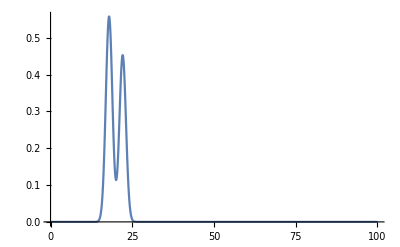

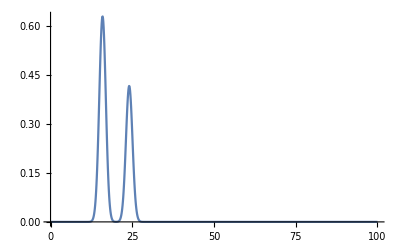

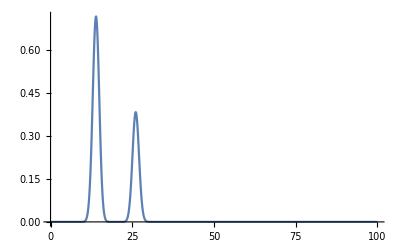

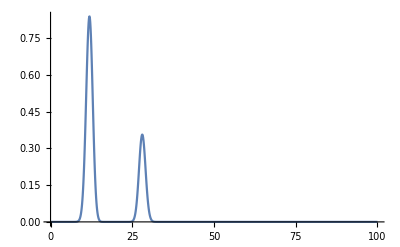

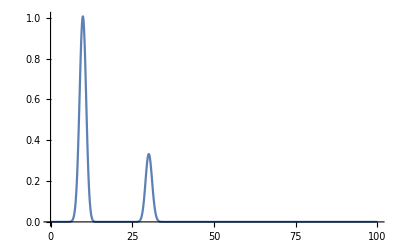

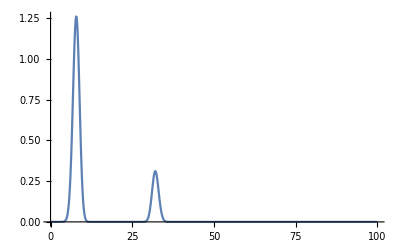

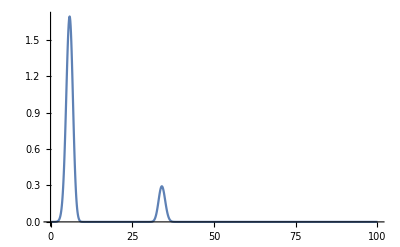

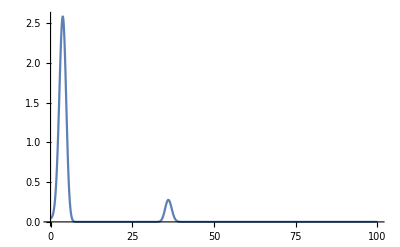

```mathematica
Do[{n=k;
sol=LinearSolve[A,-b],
Do[u[n+1,i]=sol[[i+1]],{i,0,imax}],If[Mod[n,25]==0,Print[ListPlot[Table[{r[i],u[n+1,i]},{i,0,imax}],pl=PlotRange->All,Joined->True]]]},{k,1,2000}]
```